```mathematica
Quit[];
```

```mathematica
Needs["MaTeX`"]
```

```mathematica
<<sneg`sneg`;
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

res::shdw: Symbol res appears in multiple contexts {Sneg`,Global`}; definitions in context Sneg` may shadow or be shadowed by other definitions.

```mathematica
Simp=1;
Subscript[S, 1]=spinmatrixX[Simp];
Subscript[S, 2]=spinmatrixY[Simp];
Subscript[S, 3]=spinmatrixZ[Simp];
IdS=IdentityMatrix[2Simp+1];
```

```mathematica
Subscript[σ, 3]={{1,0},{0,-1}};
Subscript[σ, 1]={{0,1},{1,0}};
Subscript[σ, 2]={{0,-I},{I,0}};
Id=IdentityMatrix[2];
```

```mathematica
h0=.4;
nvec=1/(√3){1,1,1};
h=h0 nvec;
g=1;
```

Kitaev interaction with embedded magnetic impurity.

```mathematica
kronk=Fold[KroneckerProduct];
Hz[Kp_]=-1/4(KroneckerProduct[Subscript[σ, 3],Subscript[σ, 3],kronk[Table[Id,5]],IdS]+KroneckerProduct[kronk[Table[Id,2]],Subscript[σ, 3],Subscript[σ, 3],kronk[Table[Id,3]],IdS]+KroneckerProduct[kronk[Table[Id,4]],Subscript[σ, 3],Subscript[σ, 3],kronk[Table[Id,1]],IdS])-1/2 Kp KroneckerProduct[kronk[Table[Id,6]],Subscript[σ, 3],Subscript[S, 3]];
Hx[Kp_]=-1/4(KroneckerProduct[Id,Subscript[σ, 1],Subscript[σ, 1],kronk[Table[Id,4]],IdS]+KroneckerProduct[Subscript[σ, 1],Id,Id,Subscript[σ, 1],kronk[Table[Id,3]],IdS]+KroneckerProduct[kronk[Table[Id,5]],Subscript[σ, 1],Subscript[σ, 1],IdS])-1/2 Kp KroneckerProduct[kronk[Table[Id,4]],Subscript[σ, 1],Id,Id,Subscript[S, 1]];
Hy[Kp_]=-1/4(KroneckerProduct[Id,Subscript[σ, 2],Id,Id,Subscript[σ, 2],kronk[Table[Id,2]],IdS]+KroneckerProduct[Subscript[σ, 2],kronk[Table[Id,4]],Subscript[σ, 2],kronk[Table[Id,1]],IdS]+KroneckerProduct[kronk[Table[Id,3]],Subscript[σ, 2],Id,Id,Subscript[σ, 2],IdS])-1/2 Kp KroneckerProduct[Id,Id,Subscript[σ, 2],kronk[Table[Id,4]],Subscript[S, 2]];
HZeeman=-Sum[h[[n]](1/2(KroneckerProduct[Subscript[σ, n],Id,Id,Id,Id,Id,Id,IdS]+KroneckerProduct[Id,Subscript[σ, n],Id,Id,Id,Id,Id,IdS]+KroneckerProduct[Id,Id,Subscript[σ, n],Id,Id,Id,Id,IdS]+KroneckerProduct[Id,Id,Id,Subscript[σ, n],Id,Id,Id,IdS]+KroneckerProduct[Id,Id,Id,Id,Subscript[σ, n],Id,Id,IdS]+KroneckerProduct[Id,Id,Id,Id,Id,Subscript[σ, n],Id,IdS]+KroneckerProduct[Id,Id,Id,Id,Id,Id,Subscript[σ, n],IdS])+g KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Subscript[S, n]]),{n,1,3}];
```

```mathematica
H[Kp_]=Hx[Kp]+Hy[Kp]+Hz[Kp]+HZeeman;
listE[Kp_]:=Sort[Eigenvalues[N[H[Kp]]]]-Sort[Eigenvalues[N[H[Kp]]]][[1]];
dim=Length[H[0]]
```

384

```mathematica
Hstrong=-KroneckerProduct[Subscript[σ, 1],Id,Id,Subscript[S, 1]]-KroneckerProduct[Id,Subscript[σ, 2],Id,Subscript[S, 2]]-KroneckerProduct[Id,Id,Subscript[σ, 3],Subscript[S, 3]];
Eigenvalues[Hstrong]//N
```

{-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,-1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Ns=50;
Kpmax=2;
dKp=Kpmax/Ns;
For[i=0,i≤Ns,i++,
Kp0=i dKp;
En=listE[Kp0];
For[j=1,j≤dim,j++,
levelsK[i,j]={Kp0,En[[j]]}]];
```

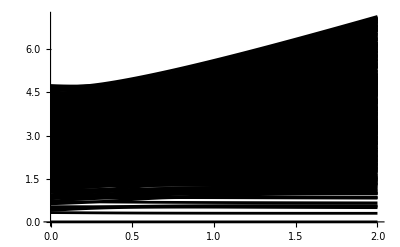

```mathematica
gspec1=ListPlot[Table[Table[levelsK[i,j],{i,0,Ns}],{j,0,dim}],PlotStyle->{Black},Joined->True]
```

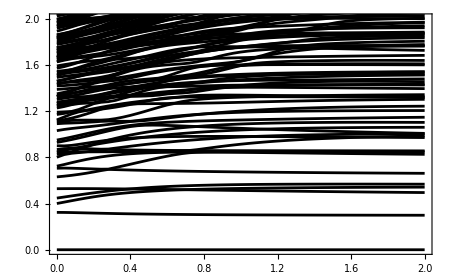

```mathematica
Kitaev=Show[gspec1,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"K'/K","\\omega/K"},ImageSize->450,PlotRange->{0,2},PlotLabel->(MaTeX["\\mathbf{h}=0.4K\\hat{\\mathbf{c}},\,g=1,\,S_{\\text{imp}}=5/2",Magnification->1.8])]
```

Heisenberg interaction with embedded magnetic impurity.

```mathematica
kronk=Fold[KroneckerProduct];
Hz[J_]=-1/4(KroneckerProduct[Subscript[σ, 3],Subscript[σ, 3],kronk[Table[Id,5]],IdS]+KroneckerProduct[kronk[Table[Id,2]],Subscript[σ, 3],Subscript[σ, 3],kronk[Table[Id,3]],IdS]+KroneckerProduct[kronk[Table[Id,4]],Subscript[σ, 3],Subscript[σ, 3],kronk[Table[Id,1]],IdS])+1/2 J Sum[KroneckerProduct[kronk[Table[Id,6]],Subscript[σ, n],Subscript[S, n]],{n,1,3}];
Hx[Kp_]=-1/4(KroneckerProduct[Id,Subscript[σ, 1],Subscript[σ, 1],kronk[Table[Id,4]],IdS]+KroneckerProduct[Subscript[σ, 1],Id,Id,Subscript[σ, 1],kronk[Table[Id,3]],IdS]+KroneckerProduct[kronk[Table[Id,5]],Subscript[σ, 1],Subscript[σ, 1],IdS])+1/2 J Sum[KroneckerProduct[kronk[Table[Id,4]],Subscript[σ, n],Id,Id,Subscript[S, n]],{n,1,3}];
Hy[J_]=-1/4(KroneckerProduct[Id,Subscript[σ, 2],Id,Id,Subscript[σ, 2],kronk[Table[Id,2]],IdS]+KroneckerProduct[Subscript[σ, 2],kronk[Table[Id,4]],Subscript[σ, 2],kronk[Table[Id,1]],IdS]+KroneckerProduct[kronk[Table[Id,3]],Subscript[σ, 2],Id,Id,Subscript[σ, 2],IdS])+1/2 J Sum[KroneckerProduct[Id,Id,Subscript[σ, n],kronk[Table[Id,4]],Subscript[S, n]],{n,1,3}];
HZeeman=-Sum[h[[n]](1/2(KroneckerProduct[Subscript[σ, n],Id,Id,Id,Id,Id,Id,IdS]+KroneckerProduct[Id,Subscript[σ, n],Id,Id,Id,Id,Id,IdS]+KroneckerProduct[Id,Id,Subscript[σ, n],Id,Id,Id,Id,IdS]+KroneckerProduct[Id,Id,Id,Subscript[σ, n],Id,Id,Id,IdS]+KroneckerProduct[Id,Id,Id,Id,Subscript[σ, n],Id,Id,IdS]+KroneckerProduct[Id,Id,Id,Id,Id,Subscript[σ, n],Id,IdS]+KroneckerProduct[Id,Id,Id,Id,Id,Id,Subscript[σ, n],IdS])+g KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Subscript[S, n]]),{n,1,3}];
H[J_]=Hx[J]+Hy[J]+Hz[J]+HZeeman;
listE[J_]:=Sort[Eigenvalues[N[H[J]]]]-Sort[Eigenvalues[N[H[J]]]][[1]];
dim=Length[H[0]]
```

384

```mathematica
Ns=50;
Jmax=0.6;
dJ=Jmax/Ns;
For[i=0,i≤Ns,i++,
J0=i dJ;
En=listE[J0];
For[j=1,j≤dim,j++,
levelsH[i,j]={J0,En[[j]]}]];
gspec2=ListPlot[Table[Table[levelsH[i,j],{i,0,Ns}],{j,0,dim}],PlotStyle->Blue,Joined->True];
```

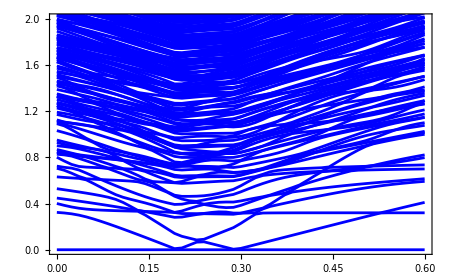

```mathematica
Heis=Show[gspec2,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J/K","\\omega/K"},ImageSize->450,PlotRange->{0,2},PlotLabel->(MaTeX["\\mathbf{h}=0.4K\\hat{\\mathbf{c}},\,g=1,\,S_{\\text{imp}}=1",Magnification->1.8])]
```

```mathematica
cvec=1/(√3){1,1,1};
Ns=50;
Jmax=0.6;
dJ=Jmax/Ns;
For[i=0,i≤Ns,i++,
J0=i dJ;
En=listE[J0];
R=Chop[Eigensystem[N[H[J0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[J0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Sum[cvec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mneigh=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Sum[cvec[[n]] 1/2 Subscript[σ, n],{n,1,3}],Id,Id,Id,Id,IdS].Ψ[1];
Mimplist[i]=Chop[N[{J0,Mimp}]];
Mneighlist[i]=Chop[N[{J0,Mneigh}]];];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMneigh=Table[Mneighlist[i],{i,0,Ns}];
```

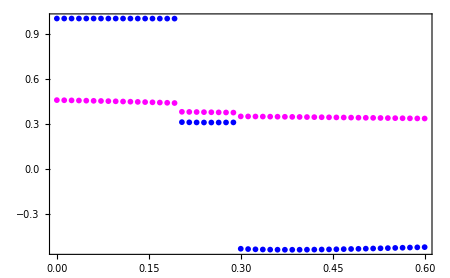

```mathematica
ListPlot[{listMimp,listMneigh},PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{c}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->2]&)/@{"\\text{impurity}","\\text{neighbor}"},{.8,.82}],PlotLabel->(MaTeX["\\mathbf{h}=0.4K\\hat{\\mathbf{c}},\,g=1,\,S_{\\text{imp}}=1",Magnification->1.8])]
```

```mathematica
avec=1/(√6){1,1,-2};
Ns=50;
Jmax=0.6;
dJ=Jmax/Ns;
For[i=0,i≤Ns,i++,
J0=i dJ;
En=listE[J0];
R=Chop[Eigensystem[N[H[J0]]]];
sortR=SortBy[Table[{R[[1,i]],R[[2,i]]},{i,1,Length[H[J0]]}],First];
Ψ[n_]:=sortR[[n,2]];
Mimp=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Id,Id,Id,Id,Id,Sum[avec[[n]] Subscript[S, n],{n,1,3}]].Ψ[1];
Mneigh=Conjugate[Ψ[1]].KroneckerProduct[Id,Id,Sum[avec[[n]] 1/2 Subscript[σ, n],{n,1,3}],Id,Id,Id,Id,IdS].Ψ[1];
Mimplist[i]=Chop[N[{J0,Mimp}]];
Mneighlist[i]=Chop[N[{J0,Mneigh}]];];
listMimp=Table[Mimplist[i],{i,0,Ns}];
listMneigh=Table[Mneighlist[i],{i,0,Ns}];
```

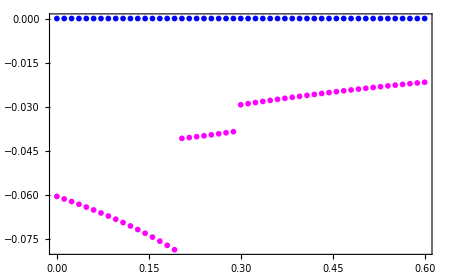

```mathematica
ListPlot[{listMimp,listMneigh},PlotStyle->{Blue,Magenta},Joined->False,Frame->True,FrameStyle->Directive[Black,16,Thickness[.002]],FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\langle \\mathbf S\\cdot \\hat{\\mathbf{a}}\\rangle"},ImageSize->450,PlotLegends->Placed[(MaTeX[#,Magnification->2]&)/@{"\\text{impurity}","\\text{neighbor}"},{.8,.25}],PlotLabel->(MaTeX["\\mathbf{h}=0.4K\\hat{\\mathbf{c}},\,g=1,\,S_{\\text{imp}}=1",Magnification->1.8])]
```